```mathematica
data={
Labeled[1,Framed["Dirichlet Series"]],Labeled[2,Framed["Mellin Transform"]],Labeled[3,Framed["Functional Equation"]],Labeled[4,Framed["Euler Product"]],Labeled[5,Framed["Jacobi ψ"]],Labeled[6,Framed["Special values"]],Labeled[7,Framed["Complex Zeros"]],Labeled[8,Framed["Hadamard Product"]],Labeled[9,Framed["RH"]],Labeled[10,Framed["N(T)"]],Labeled[11,Framed["N_0(T)"]],Labeled[12,Framed["Continuation"]],Labeled[13,Framed["Stirling"]],Labeled[14,Framed["π(x) vs Li(x)"]],Labeled[15,Framed["PNT"]],Labeled[16,Framed["Selberg Moments"]],Labeled[17,Framed["Nicolas Identity"]],Labeled[18,Framed["N(σ,T)"]]
}
```

{1Dirichlet Series,2Mellin Transform,3Functional Equation,4Euler Product,5Jacobi ψ,6Special values,7Complex Zeros,8Hadamard Product,9RH,10N(T),11N_0(T),12Continuation,13Stirling,14π(x) vs Li(x),15PNT,16Selberg Moments,17Nicolas Identity,18N(σ,T)}

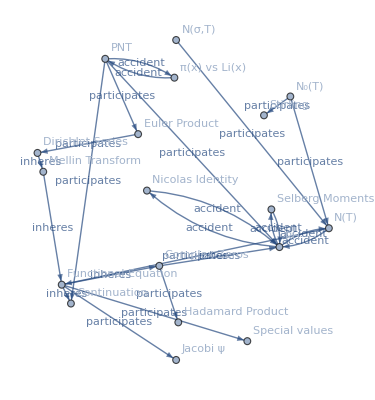

```mathematica
Graph[data,{Labeled[1->2,"inheres"],Labeled[2-> 3,"inheres"],Labeled[4-> 1,"participates"],Labeled[3-> 5,"participates"],Labeled[3-> 6,"participates"],Labeled[3-> 7,"inheres"],Labeled[7-> 8,"participates"],Labeled[7-> 9,"inheres"],Labeled[10-> 3,"participates"],Labeled[11-> 10,"participates"],Labeled[3-> 12,"inheres"],Labeled[10-> 9,"accident"],Labeled[9-> 10,"accident"],Labeled[11-> 13,"participates"],Labeled[14-> 15,"accident"],Labeled[15-> 14,"accident"],Labeled[15-> 9,"participates"],Labeled[15-> 4,"participates"],Labeled[15-> 12,"participates"],Labeled[9-> 16,"accident"],Labeled[16-> 9,"accident"],Labeled[17-> 9,"accident"],Labeled[9-> 17,"accident"],Labeled[18-> 10,"participates"]},GraphLayout->"SpiralEmbedding"]
```